# Comparação de Método de Redução de Feixe

## Caso1 -- LT com feixe regular

```mathematica
rf=0.0108965;
rpr=0.004755;
nfeixe=4;
nfases=3;
npr=2;
ϵ=8.854 10^(-12);
```

```mathematica
xy2={{-8.25,13.5275}, {-8.25, 13.5275-.50}, {-8.+.25,13.5275}, {-8.+.25,13.5275-.5}, {-0.25, 13.5275},
{-0.25,13.5275-0.5}, {0.25,13.5275}, {0.25,13.5275-0.500}, {8-.25,13.5275}, {8-.25,13.5275-.50}, {8.25,13.5275},
{8.25,13.5275-.5}, {-7.0, 24.0}, {7.0, 24.0}};
```

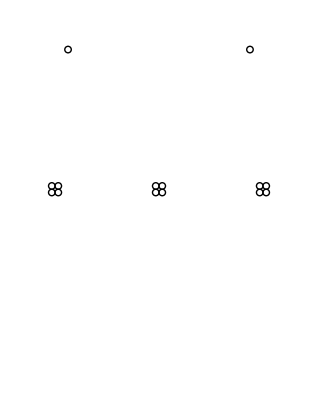

```mathematica
mostra2={Circle[#,.25]}&/@xy2;
t2=Show[Graphics[mostra2],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},{-.10,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

### Por redução matricial

```mathematica
ncond=Length[xy2];
xc=xy2[[All,1]];
yc=xy2[[All,2]]
```

{13.5275,13.0275,13.5275,13.0275,13.5275,13.0275,13.5275,13.0275,13.5275,13.0275,13.5275,13.0275,24.,24.}

```mathematica
P=Table[If[i≠j,Log[(√((xc[[i]]-xc[[j]])^2+(yc[[i]]+yc[[j]])^2))/(√((xc[[i]]-xc[[j]])^2+(yc[[i]]-yc[[j]])^2))],
If[i≤ncond-npr,Log[2 yc[[i]]/rf],Log [2 yc[[i]]/rpr]]],{i,1,ncond},{j,1,ncond}];
```

```mathematica
MatrixForm[Pinv=Inverse[P]]
```

(0.205641 | -0.0577966 | -0.0577078 | -0.0337576 | -0.00310881 | -0.00293343 | -0.00241733 | -0.00225821 | -0.000864037 | -0.000792616 | -0.000753262 | -0.000684909 | -0.00646912 | -0.00231368
-0.0577966 | 0.205853 | -0.0337638 | -0.0575061 | -0.00294337 | -0.00295214 | -0.00226997 | -0.00226606 | -0.000793318 | -0.0007522 | -0.000684909 | -0.000643885 | -0.00509024 | -0.00190531
-0.0577078 | -0.0337638 | 0.206048 | -0.0574002 | -0.00397813 | -0.00378561 | -0.00302676 | -0.00285398 | -0.00100308 | -0.000929111 | -0.000864037 | -0.000793318 | -0.00627817 | -0.00246183
-0.0337576 | -0.0575061 | -0.0574002 | 0.20624 | -0.00379361 | -0.00382181 | -0.00286385 | -0.00287526 | -0.000929111 | -0.00088886 | -0.000792616 | -0.0007522 | -0.00488978 | -0.00203052
-0.00310881 | -0.00294337 | -0.00397813 | -0.00379361 | 0.206515 | -0.0569429 | -0.0570615 | -0.0331299 | -0.00302676 | -0.00286385 | -0.00241733 | -0.00226997 | -0.00451759 | -0.00410911
-0.00293343 | -0.00295214 | -0.00378561 | -0.00382181 | -0.0569429 | 0.206685 | -0.0331299 | -0.056892 | -0.00285398 | -0.00287526 | -0.00225821 | -0.00226606 | -0.00354834 | -0.00319211
-0.00241733 | -0.00226997 | -0.00302676 | -0.00286385 | -0.0570615 | -0.0331299 | 0.206515 | -0.0569429 | -0.00397813 | -0.00379361 | -0.00310881 | -0.00294337 | -0.00410911 | -0.00451759
-0.00225821 | -0.00226606 | -0.00285398 | -0.00287526 | -0.0331299 | -0.056892 | -0.0569429 | 0.206685 | -0.00378561 | -0.00382181 | -0.00293343 | -0.00295214 | -0.00319211 | -0.00354834
-0.000864037 | -0.000793318 | -0.00100308 | -0.000929111 | -0.00302676 | -0.00285398 | -0.00397813 | -0.00378561 | 0.206048 | -0.0574002 | -0.0577078 | -0.0337638 | -0.00246183 | -0.00627817
-0.000792616 | -0.0007522 | -0.000929111 | -0.00088886 | -0.00286385 | -0.00287526 | -0.00379361 | -0.00382181 | -0.0574002 | 0.20624 | -0.0337576 | -0.0575061 | -0.00203052 | -0.00488978
-0.000753262 | -0.000684909 | -0.000864037 | -0.000792616 | -0.00241733 | -0.00225821 | -0.00310881 | -0.00293343 | -0.0577078 | -0.0337576 | 0.205641 | -0.0577966 | -0.00231368 | -0.00646912
-0.000684909 | -0.000643885 | -0.000793318 | -0.0007522 | -0.00226997 | -0.00226606 | -0.00294337 | -0.00295214 | -0.0337638 | -0.0575061 | -0.0577966 | 0.205853 | -0.00190531 | -0.00509024
-0.00646912 | -0.00509024 | -0.00627817 | -0.00488978 | -0.00451759 | -0.00354834 | -0.00410911 | -0.00319211 | -0.00246183 | -0.00203052 | -0.00231368 | -0.00190531 | 0.115612 | -0.0110483
-0.00231368 | -0.00190531 | -0.00246183 | -0.00203052 | -0.00410911 | -0.00319211 | -0.00451759 | -0.00354834 | -0.00627817 | -0.00488978 | -0.00646912 | -0.00509024 | -0.0110483 | 0.115612)

```mathematica
Pspr=Inverse[Take[Pinv,ncond-npr,ncond-npr]];  (* elimina cabo pr*)
aux02=Inverse[Pspr];
Cfase=2.0 π ϵ Table[Sum[aux02[[i,j]] ,{i,nfeixe*m -(nfeixe-1),nfeixe*m},{j,nfeixe*n -(nfeixe-1),nfeixe*n}],{m,1,nfases},{n,1,nfases}];
(* elimina feixe *)
```

### Por raio médio geométrico

Feixe circular

```mathematica
rmg1=(rf 4 Sqrt[.25^2+.25^2]^3)^(1/4)
```

0.209497

```mathematica
s=(.5)/(2 Sin[45 Degree])
```

0.353553

```mathematica
(rf 4 s^3)^(1/4)
```

0.209497

```mathematica
Total[xc[[Range[4]]]]/4
```

-8.

```mathematica
xcr={Total[xc[[Range[4]]]]/4,Total[xc[[Range[5,8]]]]/4,Total[xc[[Range[9,12]]]]/4,xc[[13]],xc[[14]]}
```

{-8.,0.,8.,-7.,7.}

```mathematica
ycr={Total[yc[[Range[4]]]]/4,Total[yc[[Range[5,8]]]]/4,Total[yc[[Range[9,12]]]]/4,yc[[13]],yc[[14]]}
```

{13.2775,13.2775,13.2775,24.,24.}

```mathematica
Prmg=Table[If[i≠j,Log[(√((xcr[[i]]-xcr[[j]])^2+(ycr[[i]]+ycr[[j]])^2))/(√((xcr[[i]]-xcr[[j]])^2+(ycr[[i]]-ycr[[j]])^2))],
If[i≤3,Log[2 yc[[i]]/rmg1],Log [2 yc[[i]]/rpr]]],{i,1,5},{j,1,5}];
```

```mathematica
PrmgInv=Inverse[Prmg]
```

{{0.227326,-0.0478614,-0.0124763,-0.0242867,-0.00910218},{-0.0478614,0.239429,-0.0478708,-0.0165313,-0.0164463},{-0.0124763,-0.0478708,0.227307,-0.00915651,-0.024169},{-0.0242867,-0.0165313,-0.00915651,0.124463,-0.0127445},{-0.00910218,-0.0164463,-0.024169,-0.0127445,0.123888}}

```mathematica
Crmg=2 π ϵ PrmgInv[[Range[3],Range[3]]]
```

{{1.26464×10^-11,-2.66259×10^-12,-6.94071×10^-13},{-2.66259×10^-12,1.33197×10^-11,-2.66311×10^-12},{-6.94071×10^-13,-2.66311×10^-12,1.26454×10^-11}}

```mathematica
MatrixForm[Crmg]
```

(1.26464×10^-11 | -2.66259×10^-12 | -6.94071×10^-13
-2.66259×10^-12 | 1.33197×10^-11 | -2.66311×10^-12
-6.94071×10^-13 | -2.66311×10^-12 | 1.26454×10^-11)

### Comparação

```mathematica
MatrixForm[Crmg 10^ 9]
```

(0.0126464 | -0.00266259 | -0.000694071
-0.00266259 | 0.0133197 | -0.00266311
-0.000694071 | -0.00266311 | 0.0126454)

```mathematica
MatrixForm[Cfase 10^9]
```

(0.0126793 | -0.00267856 | -0.000718839
-0.00267856 | 0.0132515 | -0.00267856
-0.000718839 | -0.00267856 | 0.0126793)

```mathematica
MatrixForm[10^12(Crmg- Cfase)]
```

(-0.165013 | -0.0197941 | 0.0590157
-0.0197941 | 0.269884 | -0.0216019
0.0590157 | -0.0216019 | -0.168613)

```mathematica
cp1=10 ^9 Tr[Cfase ]/3;
cm1=10^9/3(Cfase[[1,2]]+Cfase[[1,3]]+Cfase[[2,3]]);
cp1RMG=Tr[Crmg 10^ 9]/3;
cm1RMG=10^9/3(Crmg[[1,2]]+Crmg[[1,3]]+Crmg[[2,3]]);
```

```mathematica
cpos=(cp1-cm1)
```

0.0148954

```mathematica
100(0.014895383293096304-0.014666996751634676)/0.0148954
```

1.53327

```mathematica
cposRMG=(cp1RMG-cm1RMG)
```

0.0148771

```mathematica
czero=(cp1+2cm1)
```

0.00881943

```mathematica
czeroRMG=(cp1RMG+2cm1RMG)
```

0.00885732

## Caso2 -- LT com feixe expandido regular

```mathematica
rf=0.0108965;
rpr=0.004755;
nfeixe=4;
nfases=3;
npr=2;
ϵ=8.854 10^(-12);
```

```mathematica
xy2={{-8.25,13.5275}, {-8.25, 13.5275-1.50}, {-8.+.25,13.5275}, {-8.+.25,13.5275-1.5}, {-0.25, 13.5275},
{-0.25,13.5275-1.5}, {0.25,13.5275}, {0.25,13.5275-1.500}, {8-.25,13.5275}, {8-.25,13.5275-1.50}, {8.25,13.5275},
{8.25,13.5275-1.5}, {-7.0, 24.0}, {7.0, 24.0}};
```

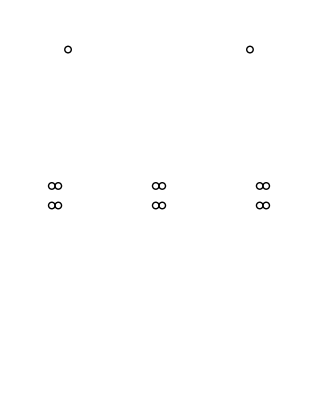

```mathematica
mostra2={Circle[#,.25]}&/@xy2;
t2=Show[Graphics[mostra2],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},{-.10,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

### Por redução matricial

```mathematica
ncond=Length[xy2];
xc=xy2[[All,1]];
yc=xy2[[All,2]]
```

{13.5275,12.0275,13.5275,12.0275,13.5275,12.0275,13.5275,12.0275,13.5275,12.0275,13.5275,12.0275,24.,24.}

```mathematica
P=Table[If[i≠j,Log[(√((xc[[i]]-xc[[j]])^2+(yc[[i]]+yc[[j]])^2))/(√((xc[[i]]-xc[[j]])^2+(yc[[i]]-yc[[j]])^2))],
If[i≤ncond-npr,Log[2 yc[[i]]/rf],Log [2 yc[[i]]/rpr]]],{i,1,ncond},{j,1,ncond}];
```

```mathematica
Pinv=Inverse[P];
```

```mathematica
Pspr=Inverse[Take[Pinv,ncond-npr,ncond-npr]];  (* elimina cabo pr*)
aux02=Inverse[Pspr];
Cfase=2.0 π ϵ Table[Sum[aux02[[i,j]] ,{i,nfeixe*m -(nfeixe-1),nfeixe*m},{j,nfeixe*n -(nfeixe-1),nfeixe*n}],{m,1,nfases},{n,1,nfases}];
(* elimina feixe *)
```

### Por raio médio geométrico

Como o feixe não é simétrico, é necessário adaptar a formulação do RMG

```mathematica
rmg1=(rf .5 √(.5^2+1.5^2)1.5)^(1/4)
```

0.337155

```mathematica
Total[xc[[Range[4]]]]/4
```

-8.

```mathematica
xcr={Total[xc[[Range[4]]]]/4,Total[xc[[Range[5,8]]]]/4,Total[xc[[Range[9,12]]]]/4,xc[[13]],xc[[14]]}
```

{-8.,0.,8.,-7.,7.}

```mathematica
ycr={Total[yc[[Range[4]]]]/4,Total[yc[[Range[5,8]]]]/4,Total[yc[[Range[9,12]]]]/4,yc[[13]],yc[[14]]}
```

{12.7775,12.7775,12.7775,24.,24.}

```mathematica
Prmg=Table[If[i≠j,Log[(√((xcr[[i]]-xcr[[j]])^2+(ycr[[i]]+ycr[[j]])^2))/(√((xcr[[i]]-xcr[[j]])^2+(ycr[[i]]-ycr[[j]])^2))],
If[i≤3,Log[2 yc[[i]]/rmg1],Log [2 yc[[i]]/rpr]]],{i,1,5},{j,1,5}];
```

```mathematica
PrmgInv=Inverse[Prmg];
```

```mathematica
Crmg=2 π ϵ PrmgInv[[Range[3],Range[3]]]
```

{{1.41843×10^-11,-3.33101×10^-12,-7.48227×10^-13},{-3.33101×10^-12,1.53957×10^-11,-3.33282×10^-12},{-7.48227×10^-13,-3.33282×10^-12,1.41807×10^-11}}

### Comparação

```mathematica
MatrixForm[Crmg 10^ 9]
```

(0.0141843 | -0.00333101 | -0.000748227
-0.00333101 | 0.0153957 | -0.00333282
-0.000748227 | -0.00333282 | 0.0141807)

```mathematica
MatrixForm[Cfase 10^9]
```

(0.0143493 | -0.00331122 | -0.000807243
-0.00331122 | 0.0151258 | -0.00331122
-0.000807243 | -0.00331122 | 0.0143493)

```mathematica
cp1=10 ^9 Tr[Cfase ]/3;
cm1=10^9/3(Cfase[[1,2]]+Cfase[[1,3]]+Cfase[[2,3]]);
cp1RMG=Tr[Crmg 10^ 9]/3;
cm1RMG=10^9/3(Crmg[[1,2]]+Crmg[[1,3]]+Crmg[[2,3]]);
```

```mathematica
cpos=(cp1-cm1)
```

0.0170847

```mathematica
cposRMG=(cp1RMG-cm1RMG)
```

0.0170576

```mathematica
czero=(cp1+2cm1)
```

0.00965502

```mathematica
czeroRMG=(cp1RMG+2cm1RMG)
```

0.00964552

c_1=2π ϵ 1/(Log(DMG/RMG hmg/HMG))
DM G - distância média entre os condutores,
RMG - raio médio geométrico dos condutores de fase
 hmg  - distância média geométrica entre condutores em relação às imagens de mesma fase
 HMG - dos condutores em relação às imagens de condutores de outras